```mathematica
example
```

<|length→11,ring→False,left terminator→{0,0},right terminator→{8.33779,3.49506},internal particles→{{0.52544,0.85083},{1.24058,1.54981},{1.96304,2.24123},{2.78941,2.80436},{3.55596,3.44654},{4.43675,3.92005},{5.41889,4.10816},{6.41673,4.04234},{7.36355,3.72061}},bounding region→Parallelogram[{-0.719855,1.5999},{{0.815803,-1.81315},{8.24184,3.70831}}],region member→RegionMemberFunction[Parallelogram[{-0.719855, 1.5999}, {{0.815803, -1.81315}, {8.24184, 3.70831}}], <>],nearest function→NearestFunction[…],center of mass→{3.82256,2.74354}|>

```mathematica
Graphics[polymerGraphic[example]]
```

-Graphics-

```mathematica
positions =  Join[
{example["left terminator"]},
example["internal particles"],
{example["right terminator"]}]
```

{{0,0},{0.52544,0.85083},{1.24058,1.54981},{1.96304,2.24123},{2.78941,2.80436},{3.55596,3.44654},{4.43675,3.92005},{5.41889,4.10816},{6.41673,4.04234},{7.36355,3.72061},{8.33779,3.49506}}

```mathematica
randomWiggle[positions_,dr_, dα_]:=
 Block[
{newPositions = positions, 
splitAt,
right,
left,
displacement = dr AngleVector[RandomReal[2Pi]]
},
Which[Length[positions]> 2,
splitAt= RandomInteger[{2,Length[positions]-1}];
{left,right}= {positions[[1;;splitAt]],positions[[splitAt;;-1]]};
(#+dr)&/@Join[Reverse[wiggle[Reverse[left],dα]],Rest@wiggle[right,dα]],
Length[positions]==2,
TranslationTransform[displacement][RotationTransform[dα,Mean[positions]][positions]],
True,TranslationTransform[displacement][positions]
]
]
```

```mathematica
randomWiggle[positions,.1]
```

4

{{0.127008,-0.101396},{0.597397,0.781063},{1.26039,1.52969},{1.96304,2.24123},{2.78687,2.80806},{3.56947,3.43058},{4.44544,3.91296},{5.42969,4.08973},{6.4238,3.98142},{7.36183,3.63485},{8.33173,3.39133}}

```mathematica
Length[positions]
```

11

```mathematica
Length[randomWiggle[positions,.1]]
```

4

11

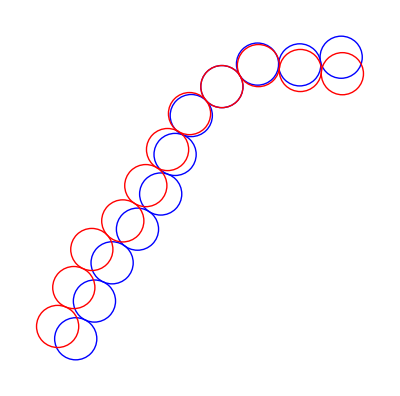

```mathematica
Graphics[
{Blue,Circle[#,1/2]&/@positions,Red,Circle[#,1/2]&/@randomWiggle[positions,.4]}]
```

```mathematica
Dynamic[Graphics[
{Blue,Circle[#,1/2]&/@positions}]]
```

```mathematica
Do[positions=randomWiggle[positions,.1];,50]
```

```mathematica
wiggle[positions_, dα_]:= Block[{
angles = ArcTan@@@Most[RotateLeft[positions]-positions],
diffs},
diffs = Prepend[Differences@angles,angles[[1]]];
(First[positions]+ #)&/@AnglePath[diffs + RandomReal[dα{-1,1}/2,Length[diffs]]]
]
```

```mathematica
Echo[{start,forwards}];
If[forwards,toWiggle = Echo@positions[[start;;-1]],toWiggle=Echo@positions[[-start;;1;;-1]]];
angles = ArcTan@@@Most[RotateLeft[toWiggle]-toWiggle];
diffs = Prepend[Differences@angles,angles[[1]]];
wiggled = AnglePath[diffs + RandomReal[dα{-1,1}/2,Length[diffs]]];
wiggled =With[{shift = positions[[start]]},
(# + shift)&/@wiggled];
If[forwards,
Join[positions[[1;;start-1]],wiggled],
Join[Reverse[wiggled],positions[[start+1;;-1]]]]
]
```

{{5.17639,2.50003},{5.68442,3.36137},{6.41673,4.04234},{7.36355,3.72061},{8.33779,3.49506}}

```mathematica
randomWiggle[]
```

```mathematica
randomMotion[chainAssociation_,dx_, dα_]:=
 Block[
{newchain = chainAssociation, positions},
positions = Join[
{newchain["left terminator"]},
newchain["internal particles"],
{newchain["right terminator"]}];
vecs  = Most[RotateLeft[positions]-positions];
angles = ArcTan@@@vecs;
diffs = Prepend[Differences@angles,angles[[1]]];
AnglePath[diffs + RandomReal[dα{-1,1}/2,Length[diffs]]]
]
```

```mathematica
randomMotion[example,.1,.1]
```

{{0.,0.},{0.52544,0.85083},{1.24058,1.54981},{1.96304,2.24123},{2.78941,2.80436},{3.55596,3.44654},{4.43675,3.92005},{5.41889,4.10816},{6.41673,4.04234},{7.36355,3.72061},{8.33779,3.49506}}

```mathematica
Prepend[Differences@randomMotion[example,.1,.1],1.017563777557325]
```

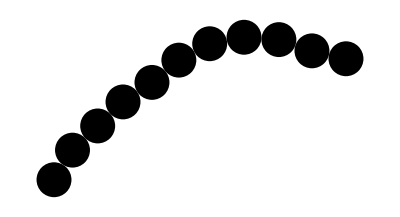

```mathematica
Graphics[Disk[#,1/2]&/@randomMotion[example,.1,.01]
]
```